#### Compute Euler Lotka estimator for the Weibull distribution

By definition, the Euler Lotka estimator corresponds to

```mathematica
ELestWei[shape_?NumericQ, scale_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[WeibullDistribution[shape, scale],t]*Exp[-r*t],{t,0,Infinity}, Method->Automatic]
```

```mathematica
ELestWeiCut10days[shape_?NumericQ, scale_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[WeibullDistribution[shape, scale],t]*Exp[-r*t],{t,0,10}, Method->Automatic]
```

Using the shape and scale values taken from Ferretti

```mathematica
FerrettiValues={shape->2.826, scale->5.665}
```

{shape→2.826,scale→5.665}

we get the following curve which the Euler-Lotka estimate of R0 as a function of the exponential growth rate r

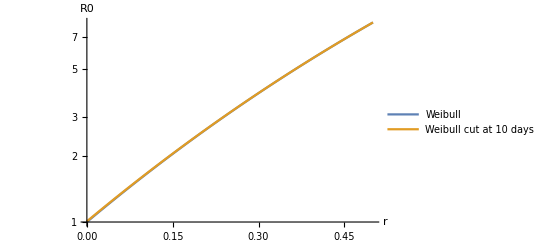

```mathematica
LogPlotWei=LogPlot[{ELestWei[shape/.FerrettiValues, scale/.FerrettiValues,r],ELestWeiCut10days[shape/.FerrettiValues, scale/.FerrettiValues,r]},{r,0,0.5}, PlotLegends->LineLegend[{"Weibull", "Weibull cut at 10 days"}], AxesLabel->{r, R0}]
```

#### Compute Euler Lotka estimator for the Lognormal distribution

The procedure is similar to the Weibull case. We start with the definition of the Euler-Lotka estimator for the lognormal distribution

```mathematica
ELestlognorm[mu_?NumericQ, sig_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[LogNormalDistribution[mu, sig],t]*Exp[-r*t],{t,0,Infinity}, Method->Automatic]
```

```mathematica
ELestlognormCut10days[mu_?NumericQ, sig_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[LogNormalDistribution[mu, sig],t]*Exp[-r*t],{t,0,Infinity}, Method->Automatic]
```

To define the lognormal parameters mu and sigma we use their relations with the median infectious time and the mean infectious time together with the values measured from Nishimura (median infectious time  of 4 days and mean infectious time of 4.7 days). This gives

```mathematica
NishimuraValues=Solve[{PowerExpand[Log[NishimuraValues=Median[LogNormalDistribution[mu,sig]]]==Log[4]], PowerExpand[Log[Mean[LogNormalDistribution[mu, sig]]]==Log[4.7]]}, {mu,sig}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{mu→1.38629,sig→0.567923}

Plugging these values into the Euler-Lotka estimator we can plot R0 as a function of the exponential growth rate, which gives

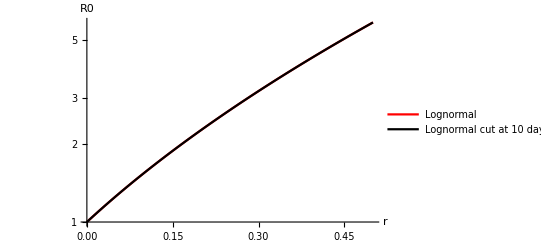

```mathematica
LogPlotlognorm=LogPlot[{ELestlognorm[mu/.NishimuraValues, sig/.NishimuraValues,r], ELestlognormCut10days[mu/.NishimuraValues, sig/.NishimuraValues,r]},{r,0,0.5}, PlotStyle->{Red, Black}, PlotLegends->LineLegend[{"Lognormal", "Lognormal cut at 10 days"}],AxesLabel->{r, R0}]
```

#### Compute Euler Lotka estimator for the SEIR model

To compute the Euler Lotka estimator for the SEIR model we first need to estimate the generation time distribution in that model. To this end we first write the equations goverining the probabilities pe(t) and pi(t) that an individual is exposed/infectious after a time t from contagion.

```mathematica
SEIReq={D[pe[t],t]==-pe[t]/tincubation, D[pi[t],t]==+pe[t]/tincubation - pi[t]/tinfection, pe[0]==1, pi[0]==0}
```

{pe'[t]==-pe[t]/tincubation,pi'[t]==pe[t]/tincubation-pi[t]/tinfection,pe[0]==1,pi[0]==0}

By definition, the generation time distribution is pi(y)/Int_0^Infinity pi(t) dt. This gives the generation time distribution for the SEIR model

```mathematica
temp=pi[t]/.DSolve[SEIReq,{pe[t], pi[t]},t][[1]]
```

(ⅇ^(-t/tincubation-t/tinfection) (-ⅇ^(t/tincubation)+ⅇ^(t/tinfection)) tinfection)/(tincubation-tinfection)

```mathematica
SEIRdistribution = Simplify[temp/Assuming[{tincubation >0, tinfection>0},Integrate[temp,{t,0,Infinity}]]]
```

(ⅇ^(-t/tincubation)-ⅇ^(-t/tinfection))/(tincubation-tinfection)

We can then define the Euler Lotka estimator for the SEIR generation time distribution as

```mathematica
ELestSEIR = 1/Assuming[{tincubation >0, tinfection>0, r>0}, Integrate[SEIRdistribution * Exp[-r*t], {t,0,Infinity}]]
```

1+r tincubation+r tinfection+r^2 tincubation tinfection

Using the parameters that I considered for my simulation

```mathematica
SEIRValues={tincubation-> 3.5868, tinfection ->7.2042 }
```

{tincubation→3.5868,tinfection→7.2042}

We can plot the Euler Lotka estimate of R0 as a function of the exponential growth rate r.

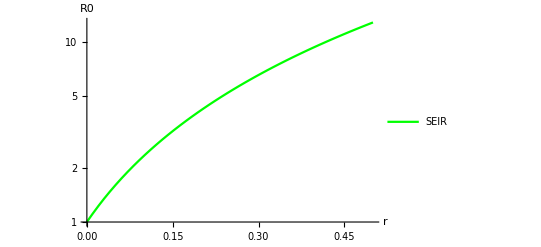

```mathematica
LogPlotSEIR=LogPlot[ELestSEIR/.SEIRValues, {r,0, 0.5}, PlotStyle->Green, PlotLegends->LineLegend[{"SEIR"}],AxesLabel->{r, R0}]
```

#### Putting results together

Putting together the results shown above, we see that the SEIR model tends to yield the highest esitmate of R0, wherease the Lognormal distribution give the smallest estimates of R0. Estimates of R0 from the Weibull distribution sits in between, but closer to the Lognormal estimates than the SEIR ones.

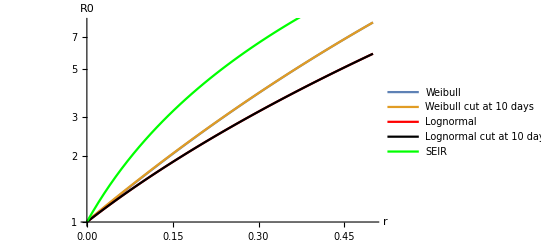

```mathematica
output1=Show[LogPlotWei, LogPlotlognorm, LogPlotSEIR,AxesLabel->{r, R0}]
```

```mathematica
Export["R0_vs_r_for_distributions.pdf",output1]
```

R0_vs_r_for_distributions.pdf

To give a bit more of perspective, I the Weibull, distribution gives R0 estimates that are 10~20% larger than the estimates from the Lognormal distribution when R0 from the Lognormal distribution falls between 2 and 3. The difference falls below 5% when R0 estimates are below 1.5.

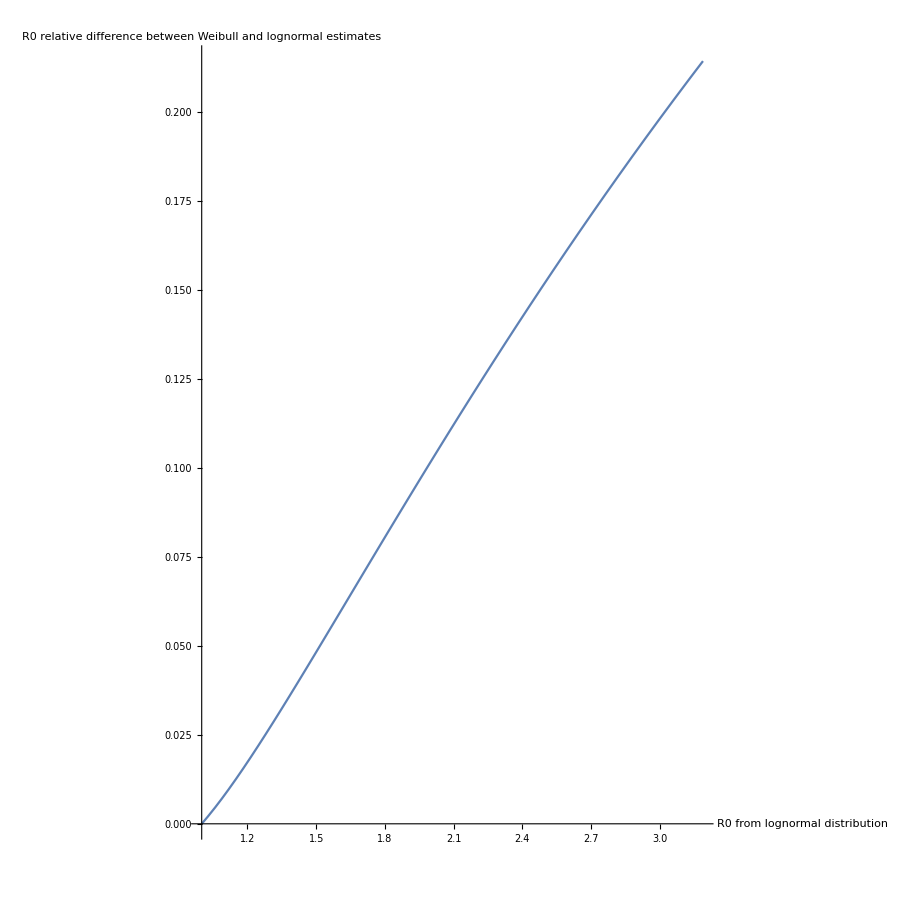

```mathematica
ParametricPlot[{ELestlognorm[mu/.NishimuraValues, sig/.NishimuraValues,r],(ELestWei[shape/.FerrettiValues, scale/.FerrettiValues,r] - ELestlognorm[mu/.NishimuraValues, sig/.NishimuraValues,r])/ELestlognorm[mu/.NishimuraValues, sig/.NishimuraValues,r]}, {r,0,0.3}, AspectRatio->1, AxesLabel->{"R0 from lognormal distribution","R0 relative difference between Weibull and lognormal estimates"}]
```

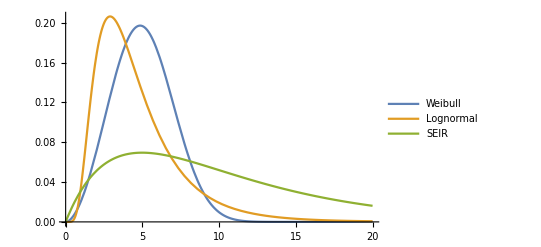

```mathematica
Plot[{PDF[WeibullDistribution[shape/.FerrettiValues, scale/.FerrettiValues],t], PDF[LogNormalDistribution[mu/.NishimuraValues, sig/.NishimuraValues],t],SEIRdistribution/.SEIRValues},{t, 0, 20}, PlotLegends->LineLegend[{"Weibull", "Lognormal", "SEIR"}]]
```